## Uniform Continuity

## Presentation of Chapter 8 Appendix, Problem 2, p. 144

-Graphics-

### 2(a) Sums

Prove that the sum of two uniformly continuous function is uniformly continuous.

Since f is uniformly continuous on A there is a δ_f such that for all xand y in A,

|f(x)-f(y)|<ϵ/2,

provided that

|x-y|<δ_f.

Similarly,

|g(x)-g(y)|<ϵ/2,

provided that

|x-y|<δ_g

Now choose δ to be the smaller of δ_f and δ_g. Then

|f(x)+g(x)-(f(y)+g(y))|<=|f(x)-f(y)|+|g(x)-g(y)|<ϵ/2+ϵ/2=ϵ

Voila.

### 2(b) Products

Prove that the product of two uniformly continuous function is uniformly continuous, provided that both functions are bounded on the interval in question.

As in 2(a), we will have a δ_f and δ_g. This time choose the ϵ for f to be ϵ/(2N). E.g., our δ_f will be sufficiently small such that 

|f(x)-f(y)|<ϵ/(2N)

where N is the bound on g. E.g., |g(x)|<N.

Similarly, choose the ϵ for g to be ϵ/(2M). E.g., our δ_g will be sufficiently small such that 

|g(x)-g(y)|<ϵ/(2M)

where M is the bound on f. E.g., |f(x)|<M.

Now we consider

|f(x)g(x)-f(y)g(y)|=|f(x)g(x)-f(y)g(x)+f(y)g(x)-f(y)g(y)|<=|f(x)g(x)-f(y)g(x)|+|f(y)g(x)-f(y)g(y)|=|f(x)-f(y)||g(x)|+|f(y)||g(x)-g(y)|<|f(x)-f(y)|N+M|g(x)-g(y)|<ϵ/(2N)N+M ϵ/(2M)=ϵ/2+ϵ/2=ϵ

Voila.

### Counterexample asked for in 2(c)

The product of two functions that are uniformly continuous may not be uniformly continuous if one of them is unbounded. Of course the only way this can happen is if the interval is unbounded, because a continuous function on a bounded interval is bounded.

Example: let f(x)=sin x and g(x)=x. Let the interval be [0,∞). Both f and g are uniformly continuous even though g is unbounded. That’s because g’s slope is constant.

Let’s graph the product:

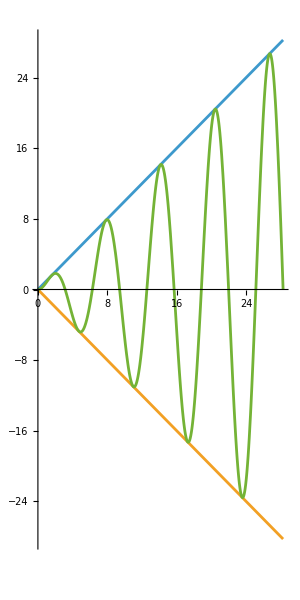

```mathematica
Plot[{x,-x,xSin[x]},{x,0,18Pi/2},AspectRatio->2]
```

Let’s consider x=2π and x=4π. Let’s consider ϵ=1. At x=2π, that means |xsin x|<1. Let’s blow up that region of the plot:

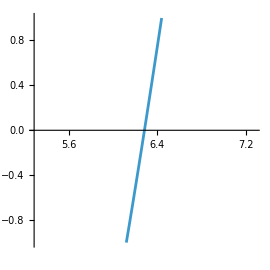

```mathematica
Plot[xSin[x],{x,2Pi-1,2Pi+1}, PlotRange->{{2Pi-1,2Pi+1},{-1,1}},AspectRatio->1]
```

Eyeballing the plot, it appears that a δ of about 0.2 will do the job for ϵ=1.

Now let’s make a similar plot but at x=4π.

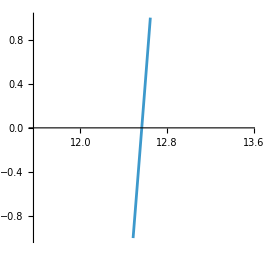

```mathematica
Plot[xSin[x],{x,4Pi-1,4Pi+1}, PlotRange->{{4Pi-1,4Pi+1},{-1,1}},AspectRatio->1]
```

It is clear that the δ of about 0.2 will not do the job because the function is steeper here (twice as steep in fact).

You could do δ of about 0.1, but then if you go out twice as far again, to x=8π, you’ll need a δ of about 0.05 because the function is twice again as steep:

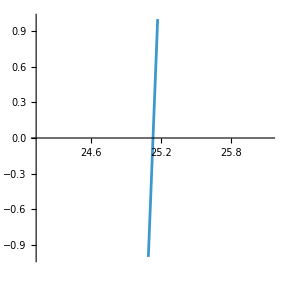

```mathematica
Plot[xSin[x],{x,8Pi-1,8Pi+1}, PlotRange->{{8Pi-1,8Pi+1},{-1,1}},AspectRatio->1]
```

### 2(d) Composition

Here again is the statement of Part (d):

-Graphics-

The proof of this is going to have to go a lot like the proof of Theorem 2 of Chapter 6 on p. 115, which starts out like this:

-Graphics-
Notice that the roles of f and g have been interchanged.

If you look at the rest of the proof of Theorem 2 of Chapter 6, you’ll see that it indeed has almost the exactly the same outline as our proof that follows:

PROOF

Because g is uniformly continuous on B we know that for f(x) and f(y) (which by assumption are in B provided x and y are in A) that there is a δ_g such that |g(f(x))-g(f(y))|<ϵ provided that |f(x)-f(y)|<δ_g.

But we also know that since f is uniformly continuous on A that there is a δ_f such that |f(x)-f(y)|<δ_g provided that |x-y|<δ_f. (δ_g is just playing the role of the ϵ in the definition of uniform continuity for f.)

To summarize: the ϵ requires a certain δ_g, and this δ_g transitively requires a certain δ_f. This δ_f is the δ we need to make

|g(f(x))-g(f(y))|<ϵ

for any x,y in A with |x-y|<δ .